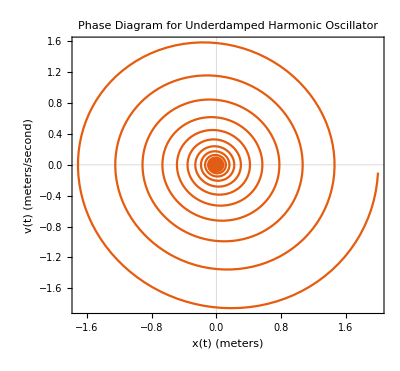

```mathematica
Remove["Global`*"]//Quiet
x[t_] = 2 Exp[-0.05 t] Cos[t];
v[t_]=x'[t];
ParametricPlot[{x[t],v[t]},{t,0,200},PlotRange->All,PlotTheme->"Scientific",PlotLabel->"Phase Diagram for Underdamped Harmonic Oscillator",FrameLabel->{"x(t) (meters)","v(t) (meters/second)"}]
```

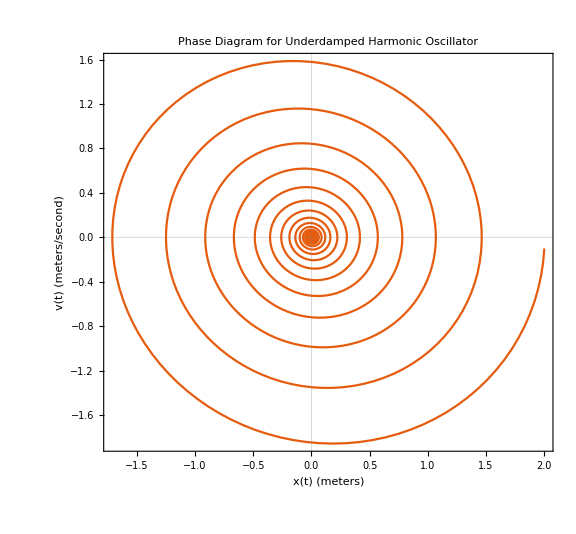

```mathematica
Show[%1953,ImageSize->Large]
```